```mathematica
f[x_,y_] := If[y == 0,x,Sin[x y]/y]
Plot3D[(f[x,y]-f[0,0])/ Sqrt[x^2 + y^2],{x,-0.1,0.1},{y,-0.1,0.1}]
```

-Graphics3D-

```mathematica
x =  2.5;
Element[x,Integers]
Element[x,Reals]
Remove[x]
sol = Solve[x^2 == -1,x];
Element[Flatten[x/.sol],Complexes]
```

False

True

True

```mathematica
a= Divisors[30]
b= Divisors[45]
Union[a,b]
c = Intersection[a,b]
Complement[a,c]
Subsets[c]
```

{1,2,3,5,6,10,15,30}

{1,3,5,9,15,45}

{1,2,3,5,6,9,10,15,30,45}

{1,3,5,15}

{2,6,10,30}

{{},{1},{3},{5},{15},{1,3},{1,5},{1,15},{3,5},{3,15},{5,15},{1,3,5},{1,3,15},{1,5,15},{3,5,15},{1,3,5,15}}

```mathematica
d = Union[a,b];
Union[Complement[d,a],Complement[d,b]] == Complement[d,Intersection[a,b]]
```

True

```mathematica
Select[Range[100],Length[Divisors[#]] == 2 &]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
#^# &[2]
```

4

```mathematica
Divisors[4]
```

{1,2,4}

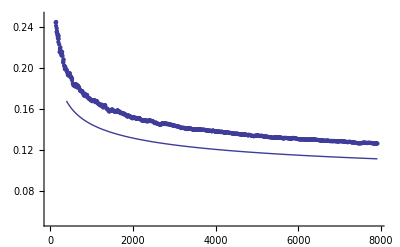

```mathematica
f[x_] = N[Integrate[a/Log[y],{y,2,x}]/x];
Show[ListPlot[Table[{Prime[n],n/Prime[n]},{n,1000}],PlotRange->{0.05,0.25}],Plot[1/Log[x],{x,1,Prime[1000]}]]
```

```mathematica
Diff[f_] = D[f,x];
Diff[x^2]
```

0

```mathematica
6>4 && -4>-8
```

True

```mathematica
6>4&&-4>-8
And[4>2,5>6]
4*2==6||3*3==9
Or[Pi>4,-3-2==5]
```

True

False

True

False

```mathematica
ForAll[x,x>10,p x+q>0]
Resolve[%,Reals]
```

∀_(x,x>10)x p+q>0

(p==0&&-q<0)||(-p<0&&-10 p-q≤0)

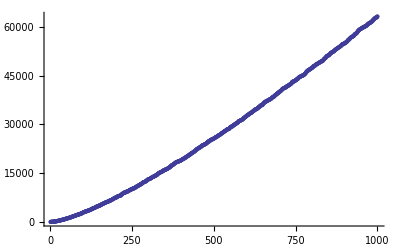

```mathematica
v[x_] := N[Sum[Log[p],{p,Prime[x]}]];
ListPlot[Table[v[n],{n,1,1000}]]
```

```mathematica
t[x_]:=Table[Prime[p],{p,x}]
Length[t[p]]
```

Table::iterb: Iterator {p, p} does not have appropriate bounds.

2

```mathematica
len[12]
```

12

```mathematica
{2,3,5,7,11}
```

```mathematica
pi[2]
```

2

```mathematica
Clear["Global`*"]
```

```mathematica
ForAll[x,a x^2 + b x + c > 0]
```

∀_x c+b x+a x^2>0

```mathematica
Resolve[Exists[x,a x^2+b x + c > 0],Reals]
```

a>0||(a==0&&b≠0)||(a==0&&c>0)||(a<0&&-b^2+4 a c<0)

```mathematica
Resolve[ForAll[x,a x^2+b x + c > 0],Reals]
```

(a==0&&b==0&&c>0)||(a≥0&&b==0&&c>0&&-b^2+4 a c>0)||(a>0&&-b^2+4 a c>0)

```mathematica
ForAll[x,Or[a y + b > 0 , c y^2 + d < 0]]
```

b+a y>0||d+c y^2<0

```mathematica
Resolve[Exists[y,Or[a y + b > 0 , c y^2 + d < 0]],Reals]
```

a≠0||b>0||d<0||(c<0&&d>0)||(c<0&&d==0)

```mathematica
pi[d_]:=Length[Select[Range[d],Length[Divisors[#] ]== 2 &]]

Cos[#]&[2 Pi]
```

```mathematica
Show[ListPlot[Table[a x + 3,{a,4}],PlotRange->{0.05,0.25}]]
```

-Graphics-

```mathematica
Show[ListPlot[{3+a 4,3+a x,3+ax,3+ax},{x,-5,5},PlotRange->{0.05,0.25}]]
```

ListPlot::nonopt: Options expected (instead of {x, -5, 5}) beyond position 1 in ListPlot[{3 + ax, 3 + ax, 3 + ax, 3 + ax}, {x, -5, 5}, PlotRange → {0.05, 0.25}]. An option must be a rule or a list of rules.

Show::gtype: ListPlot is not a type of graphics.

Show[ListPlot[{3+ax,3+ax,3+ax,3+ax},{x,-5,5},PlotRange→{0.05,0.25}]]

```mathematica
Show[ListPlot[{{{3-30 x,7+5 x^2},{4-30 x,7+5 x^2},{5-30 x,7+5 x^2},{6-30 x,7+5 x^2},{7-30 x,7+5 x^2}},{{3-29 x,7+5 x^2},{4-29 x,7+5 x^2},{5-29 x,7+5 x^2},{6-29 x,7+5 x^2},{7-29 x,7+5 x^2}},{{3-28 x,7+5 x^2},{4-28 x,7+5 x^2},{5-28 x,7+5 x^2},{6-28 x,7+5 x^2},{7-28 x,7+5 x^2}},{{3-27 x,7+5 x^2},{4-27 x,7+5 x^2},{5-27 x,7+5 x^2},{6-27 x,7+5 x^2},{7-27 x,7+5 x^2}},{{3-26 x,7+5 x^2},{4-26 x,7+5 x^2},{5-26 x,7+5 x^2},{6-26 x,7+5 x^2},{7-26 x,7+5 x^2}},{{3-25 x,7+5 x^2},{4-25 x,7+5 x^2},{5-25 x,7+5 x^2},{6-25 x,7+5 x^2},{7-25 x,7+5 x^2}},{{3-24 x,7+5 x^2},{4-24 x,7+5 x^2},{5-24 x,7+5 x^2},{6-24 x,7+5 x^2},{7-24 x,7+5 x^2}},{{3-23 x,7+5 x^2},{4-23 x,7+5 x^2},{5-23 x,7+5 x^2},{6-23 x,7+5 x^2},{7-23 x,7+5 x^2}},{{3-22 x,7+5 x^2},{4-22 x,7+5 x^2},{5-22 x,7+5 x^2},{6-22 x,7+5 x^2},{7-22 x,7+5 x^2}},{{3-21 x,7+5 x^2},{4-21 x,7+5 x^2},{5-21 x,7+5 x^2},{6-21 x,7+5 x^2},{7-21 x,7+5 x^2}},{{3-20 x,7+5 x^2},{4-20 x,7+5 x^2},{5-20 x,7+5 x^2},{6-20 x,7+5 x^2},{7-20 x,7+5 x^2}},{{3-19 x,7+5 x^2},{4-19 x,7+5 x^2},{5-19 x,7+5 x^2},{6-19 x,7+5 x^2},{7-19 x,7+5 x^2}},{{3-18 x,7+5 x^2},{4-18 x,7+5 x^2},{5-18 x,7+5 x^2},{6-18 x,7+5 x^2},{7-18 x,7+5 x^2}},{{3-17 x,7+5 x^2},{4-17 x,7+5 x^2},{5-17 x,7+5 x^2},{6-17 x,7+5 x^2},{7-17 x,7+5 x^2}},{{3-16 x,7+5 x^2},{4-16 x,7+5 x^2},{5-16 x,7+5 x^2},{6-16 x,7+5 x^2},{7-16 x,7+5 x^2}},{{3-15 x,7+5 x^2},{4-15 x,7+5 x^2},{5-15 x,7+5 x^2},{6-15 x,7+5 x^2},{7-15 x,7+5 x^2}},{{3-14 x,7+5 x^2},{4-14 x,7+5 x^2},{5-14 x,7+5 x^2},{6-14 x,7+5 x^2},{7-14 x,7+5 x^2}},{{3-13 x,7+5 x^2},{4-13 x,7+5 x^2},{5-13 x,7+5 x^2},{6-13 x,7+5 x^2},{7-13 x,7+5 x^2}},{{3-12 x,7+5 x^2},{4-12 x,7+5 x^2},{5-12 x,7+5 x^2},{6-12 x,7+5 x^2},{7-12 x,7+5 x^2}},{{3-11 x,7+5 x^2},{4-11 x,7+5 x^2},{5-11 x,7+5 x^2},{6-11 x,7+5 x^2},{7-11 x,7+5 x^2}},{{3-10 x,7+5 x^2},{4-10 x,7+5 x^2},{5-10 x,7+5 x^2},{6-10 x,7+5 x^2},{7-10 x,7+5 x^2}},{{3-9 x,7+5 x^2},{4-9 x,7+5 x^2},{5-9 x,7+5 x^2},{6-9 x,7+5 x^2},{7-9 x,7+5 x^2}},{{3-8 x,7+5 x^2},{4-8 x,7+5 x^2},{5-8 x,7+5 x^2},{6-8 x,7+5 x^2},{7-8 x,7+5 x^2}},{{3-7 x,7+5 x^2},{4-7 x,7+5 x^2},{5-7 x,7+5 x^2},{6-7 x,7+5 x^2},{7-7 x,7+5 x^2}},{{3-6 x,7+5 x^2},{4-6 x,7+5 x^2},{5-6 x,7+5 x^2},{6-6 x,7+5 x^2},{7-6 x,7+5 x^2}},{{3-5 x,7+5 x^2},{4-5 x,7+5 x^2},{5-5 x,7+5 x^2},{6-5 x,7+5 x^2},{7-5 x,7+5 x^2}},{{3-4 x,7+5 x^2},{4-4 x,7+5 x^2},{5-4 x,7+5 x^2},{6-4 x,7+5 x^2},{7-4 x,7+5 x^2}},{{3-3 x,7+5 x^2},{4-3 x,7+5 x^2},{5-3 x,7+5 x^2},{6-3 x,7+5 x^2},{7-3 x,7+5 x^2}},{{3-2 x,7+5 x^2},{4-2 x,7+5 x^2},{5-2 x,7+5 x^2},{6-2 x,7+5 x^2},{7-2 x,7+5 x^2}},{{3-x,7+5 x^2},{4-x,7+5 x^2},{5-x,7+5 x^2},{6-x,7+5 x^2},{7-x,7+5 x^2}},{{3,7+5 x^2},{4,7+5 x^2},{5,7+5 x^2},{6,7+5 x^2},{7,7+5 x^2}},{{3+x,7+5 x^2},{4+x,7+5 x^2},{5+x,7+5 x^2},{6+x,7+5 x^2},{7+x,7+5 x^2}},{{3+2 x,7+5 x^2},{4+2 x,7+5 x^2},{5+2 x,7+5 x^2},{6+2 x,7+5 x^2},{7+2 x,7+5 x^2}},{{3+3 x,7+5 x^2},{4+3 x,7+5 x^2},{5+3 x,7+5 x^2},{6+3 x,7+5 x^2},{7+3 x,7+5 x^2}},{{3+4 x,7+5 x^2},{4+4 x,7+5 x^2},{5+4 x,7+5 x^2},{6+4 x,7+5 x^2},{7+4 x,7+5 x^2}},{{3+5 x,7+5 x^2},{4+5 x,7+5 x^2},{5+5 x,7+5 x^2},{6+5 x,7+5 x^2},{7+5 x,7+5 x^2}},{{3+6 x,7+5 x^2},{4+6 x,7+5 x^2},{5+6 x,7+5 x^2},{6+6 x,7+5 x^2},{7+6 x,7+5 x^2}},{{3+7 x,7+5 x^2},{4+7 x,7+5 x^2},{5+7 x,7+5 x^2},{6+7 x,7+5 x^2},{7+7 x,7+5 x^2}},{{3+8 x,7+5 x^2},{4+8 x,7+5 x^2},{5+8 x,7+5 x^2},{6+8 x,7+5 x^2},{7+8 x,7+5 x^2}},{{3+9 x,7+5 x^2},{4+9 x,7+5 x^2},{5+9 x,7+5 x^2},{6+9 x,7+5 x^2},{7+9 x,7+5 x^2}},{{3+10 x,7+5 x^2},{4+10 x,7+5 x^2},{5+10 x,7+5 x^2},{6+10 x,7+5 x^2},{7+10 x,7+5 x^2}},{{3+11 x,7+5 x^2},{4+11 x,7+5 x^2},{5+11 x,7+5 x^2},{6+11 x,7+5 x^2},{7+11 x,7+5 x^2}},{{3+12 x,7+5 x^2},{4+12 x,7+5 x^2},{5+12 x,7+5 x^2},{6+12 x,7+5 x^2},{7+12 x,7+5 x^2}},{{3+13 x,7+5 x^2},{4+13 x,7+5 x^2},{5+13 x,7+5 x^2},{6+13 x,7+5 x^2},{7+13 x,7+5 x^2}},{{3+14 x,7+5 x^2},{4+14 x,7+5 x^2},{5+14 x,7+5 x^2},{6+14 x,7+5 x^2},{7+14 x,7+5 x^2}},{{3+15 x,7+5 x^2},{4+15 x,7+5 x^2},{5+15 x,7+5 x^2},{6+15 x,7+5 x^2},{7+15 x,7+5 x^2}},{{3+16 x,7+5 x^2},{4+16 x,7+5 x^2},{5+16 x,7+5 x^2},{6+16 x,7+5 x^2},{7+16 x,7+5 x^2}},{{3+17 x,7+5 x^2},{4+17 x,7+5 x^2},{5+17 x,7+5 x^2},{6+17 x,7+5 x^2},{7+17 x,7+5 x^2}},{{3+18 x,7+5 x^2},{4+18 x,7+5 x^2},{5+18 x,7+5 x^2},{6+18 x,7+5 x^2},{7+18 x,7+5 x^2}},{{3+19 x,7+5 x^2},{4+19 x,7+5 x^2},{5+19 x,7+5 x^2},{6+19 x,7+5 x^2},{7+19 x,7+5 x^2}},{{3+20 x,7+5 x^2},{4+20 x,7+5 x^2},{5+20 x,7+5 x^2},{6+20 x,7+5 x^2},{7+20 x,7+5 x^2}},{{3+21 x,7+5 x^2},{4+21 x,7+5 x^2},{5+21 x,7+5 x^2},{6+21 x,7+5 x^2},{7+21 x,7+5 x^2}},{{3+22 x,7+5 x^2},{4+22 x,7+5 x^2},{5+22 x,7+5 x^2},{6+22 x,7+5 x^2},{7+22 x,7+5 x^2}},{{3+23 x,7+5 x^2},{4+23 x,7+5 x^2},{5+23 x,7+5 x^2},{6+23 x,7+5 x^2},{7+23 x,7+5 x^2}},{{3+24 x,7+5 x^2},{4+24 x,7+5 x^2},{5+24 x,7+5 x^2},{6+24 x,7+5 x^2},{7+24 x,7+5 x^2}},{{3+25 x,7+5 x^2},{4+25 x,7+5 x^2},{5+25 x,7+5 x^2},{6+25 x,7+5 x^2},{7+25 x,7+5 x^2}},{{3+26 x,7+5 x^2},{4+26 x,7+5 x^2},{5+26 x,7+5 x^2},{6+26 x,7+5 x^2},{7+26 x,7+5 x^2}},{{3+27 x,7+5 x^2},{4+27 x,7+5 x^2},{5+27 x,7+5 x^2},{6+27 x,7+5 x^2},{7+27 x,7+5 x^2}},{{3+28 x,7+5 x^2},{4+28 x,7+5 x^2},{5+28 x,7+5 x^2},{6+28 x,7+5 x^2},{7+28 x,7+5 x^2}},{{3+29 x,7+5 x^2},{4+29 x,7+5 x^2},{5+29 x,7+5 x^2},{6+29 x,7+5 x^2},{7+29 x,7+5 x^2}},{{3+30 x,7+5 x^2},{4+30 x,7+5 x^2},{5+30 x,7+5 x^2},{6+30 x,7+5 x^2},{7+30 x,7+5 x^2}}},{x,-5,5}]]
```

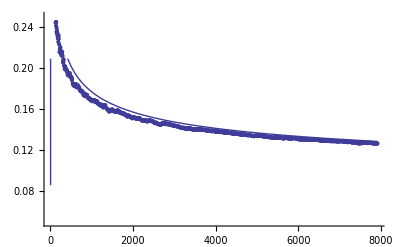

```mathematica
f[x_]=N[Integrate[1/Log[y],{y,2,x}]/x];
Show[ListPlot[Table[{Prime[n],n/Prime[n]},{n,1000}],PlotRange->{0.05,0.25}],Plot[f[x],{x,1,Prime[1000]}]]
```